```mathematica
SetDirectory[NotebookDirectory[]];
Get<<"data/SolutionVector2_Feb3";
SolutionVector01=SolutionVector2/.Null->Nothing;
BendTests=Import["data/201708_BendTests_SS_processed_data_Info.mat"];
Bendlabels=Import["data/201708_BendTests_SS_processed_data_Info.mat","Labels"]
BendTestAll=Import["data/201708_BendTests_SS_processed_data_Fw0.mat"];
BendlabelAll=Import["data/201708_BendTests_SS_processed_data_Fw0.mat","Labels"]
force= BendTestAll[[Position[BendlabelAll,"force"][[1,1]] ]];
dflctn= BendTestAll[[Position[BendlabelAll,"dflctn"][[1,1]] ]];
Bstif=Flatten[ BendTests[[Position[Bendlabels,"Bstif"][[1,1]] ]]];(*EI/L^3*)
Kcant=Flatten[ BendTests[[Position[Bendlabels,"Kcant"][[1,1]] ]]];
w0slp=Flatten[ BendTests[[Position[Bendlabels,"w0slp"][[1,1]] ]]];
w0star=Flatten[ BendTests[[Position[Bendlabels,"w0star"][[1,1]] ]]];
wsslp=Flatten[ BendTests[[Position[Bendlabels,"w_sslp"][[1,1]] ]]];
wsstar=Flatten[ BendTests[[Position[Bendlabels,"w_sstar"][[1,1]] ]]];
L=Flatten[ BendTests[[Position[Bendlabels,"L"][[1,1]] ]]];
SSpattern=Flatten[ BendTests[[Position[Bendlabels,"SSpattern"][[1,1]] ]]];
Pslip=Flatten@Position[SSpattern,True];
Pcontinue =Flatten@Position[SSpattern[[;;38]],False];
w0slpN=(w0slp/L)[[Pslip]];
w0starN=(w0star/L)[[Pslip]];
StageDis=(wsslp/L)[[Pslip]];
FailDis=(wsstar/L)[[Pslip]];
OblSlope=(Kcant/Bstif)[[Pslip]];
fw0All=Table[{dflctn[[i,j]]/L[[i]],force[[i,j]]/Bstif[[i]]/L[[i]]},{i,38},{j,Length@force[[i]]}];
fw0=fw0All[[Pslip]];
FailureIndex=Table[Length@Select[fw0[[i,;;,1]],0<#≤w0starN[[i]]&],{i,Length@w0starN}];
```

{Bstif,D,E,Fslp,Fstar,K_s,Kc_SE,Kcant,L,N_L,SSpattern,axL,dSstar,evbool,indx_fail,indx_slp,sD,s_L,w0slp,w0star,w_sslp,w_sstar}

{Fslp,Fstar,dflctn,dsplcmnt,force}

Test #1

```mathematica
NTest=1;
PSingleExp=Module[{n=NTest,P1,P2,P3},
P1 = ListPlot[fw0[[n]],PlotMarkers->{Automatic,8},PlotRange->{{0.0,0.4},{0,15}},ImageSize->1200,GridLines->None,Ticks->Automatic,Joined->True,
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False];
P2  = Module[{k = OblSlope[[n]],wss = StageDis[[n]],wsf=FailDis[[n]],Obline},
Obline[x_,wsi_] = k (wsi - x);
Plot[{Obline[x,wss],Obline[x,wsf]}, {x, 0, 0.5},PlotStyle->{Red,Purple}]
];
P3 = Module[{k = OblSlope[[n]],wss = StageDis[[n]],wsf=FailDis[[n]],Obline},
Obline[x_,wsi_] = k (wsi - x);
 Plot[Obline[x,#]&/@Range[wss,wsf,0.01], {x, 0, 0.5},PlotStyle->{Dashed,Black}]
];
Show[P1,P2,P3,Plot[48x,{x,0,0.5},PlotStyle->{Gray,Dashed}]]
];
```

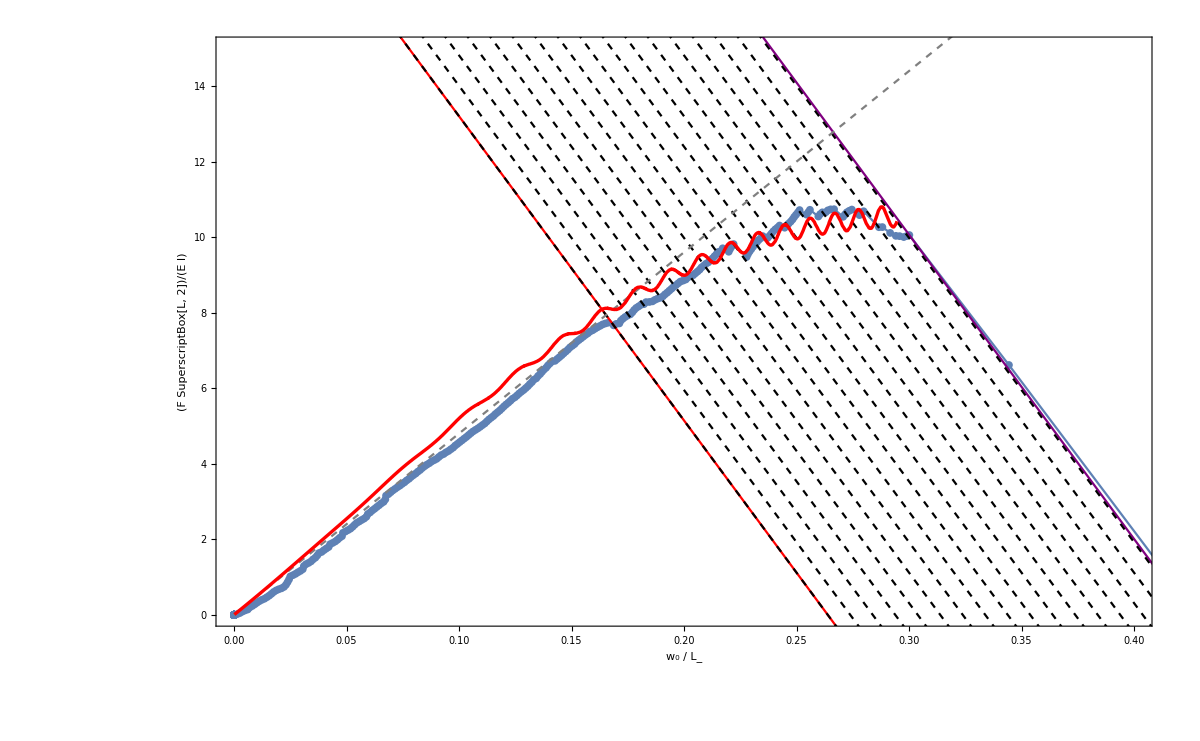

```mathematica
μ0B=0.5;
Abasis = 0.03;
λbasis=0.002;
ϕbasis=2.67035;
LengthOffset=-10;
Module[{μ0={μ0B},A = Abasis,λ=λbasis,ϕ=ϕbasis},
arclength=SolutionVector01[[;;,;;,5]];
frictionC=SolutionVector01[[;;,;;,6]];
levelset=frictionC-A Cos[arclength/λ+ϕ];
FwLevelset=Flatten[Table[{SolutionVector01[[i,j,1]],SolutionVector01[[i,j,2]],
levelset[[i,j]]},{i,1,Length@SolutionVector01},{j,1,Length[SolutionVector01[[i]]]}],1];
	Levelμ0=Table[Select[FwLevelset,Abs[#[[3]]-i]<10^-3&],{i,μ0}];
Levelμ0S=(SortBy[Levelμ0[[#]],First])&/@Range@Length@μ0;
FailIndex=Length@Select[Levelμ0S[[1,;;,1]],0<#≤w0starN[[NTest]]&]+LengthOffset;]
PVaryμ0=ListPlot[Levelμ0S[[;;,;;FailIndex,{1,2}]],
Joined->True,
PlotStyle->Directive[Red,Thickness[0.002]],ImageSize->1000,GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.4},{0,15}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6];
Show[PSingleExp,PVaryμ0]
```

```mathematica
Off[General::partw]
Lfragf[x_,k_,x0_,y0_]=-k(x-x0)+y0;
xx=fw0[[NTest,;;FailureIndex[[NTest]],1]];
yy=fw0[[NTest,;;FailureIndex[[NTest]],2]];
(*EndFail=xx[[-1]]*)
EndFail=0.274;
(*EndFail=w0starN[[NTest]]*)
Posμ0B=μ0B/0.002+1;
fitFw0B=Module[{data1,fit},
data1=SolutionVector01[[Posμ0B,;;,{1,2}]];
fit[x_]=Fit[data1,{x,x^2,x^3,x^4,x^5,x^6},x];
Function[x,fit[x]]
];
fitSw0B=Module[{data1,fit},
data1=SolutionVector01[[Posμ0B,;;,{1,5}]];
fit[x_]=Fit[data1,{1,x,x^2,x^3},x];
Function[x,fit[x]]
];
fitVariation=Module[{ λ=λbasis,ϕ=ϕbasis,xx1,yy1,data1,ABF},
xx1=fitSw0B/@Levelμ0S[[1,;;,1]];
yy1=Levelμ0S[[1,;;,2]]-fitFw0B/@Levelμ0S[[1,;;,1]];
data1=Transpose@{xx1,yy1};
ABF=FindFit[data1,(B1 x +B2 x^2 +B3 x^3 +B4 x^4 + B5 x^5+B6 x^6   +B7 x^7 +B8 x^8 )Cos[x/λ+ϕ],{B1,B2,B3,B4,B5,B6,B7,B8},x];
Function[x,Evaluate[(B1 x +B2 x^2 +B3 x^3 +B4 x^4 + B5 x^5 +B6 x^6 +B7 x^7 +B8 x^8 (*+B9 x^9+B10 x^10*) )Cos[x/λ+ϕ]/.ABF]]
];
```

### The real path for slope of Test#1

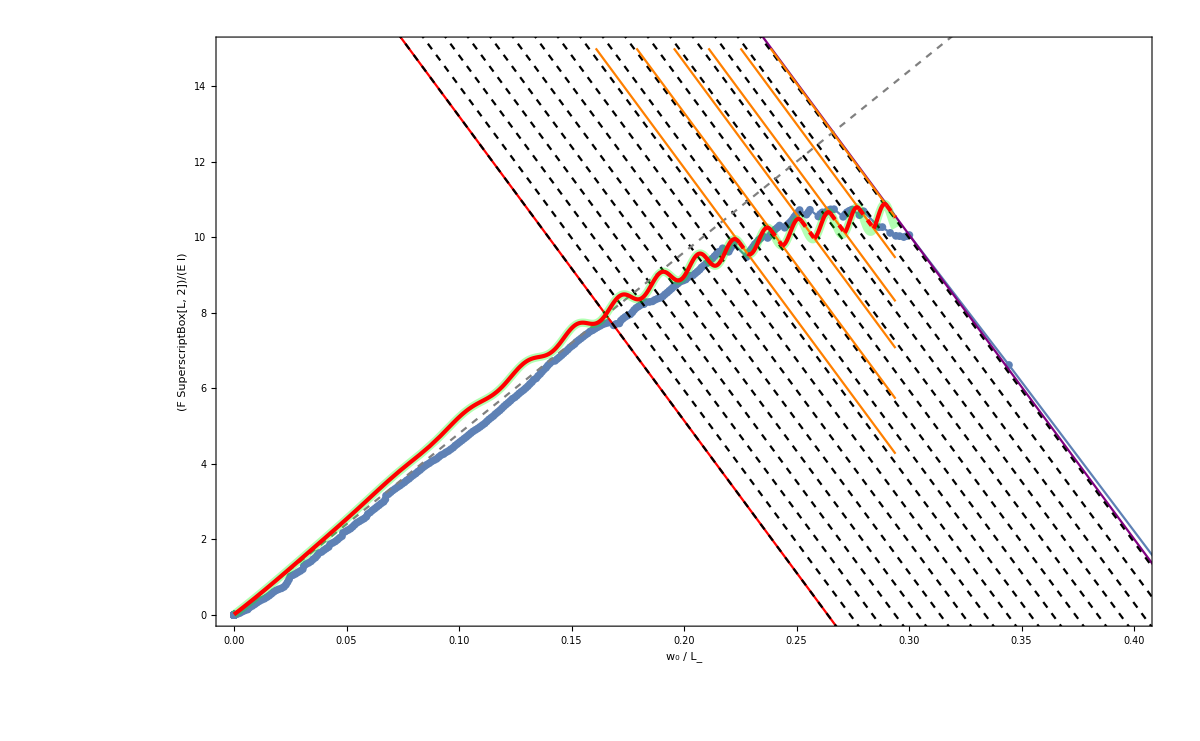

6.66787

```mathematica
EndFailOffset=0.02;
Pffrag=Module[{f,IntSecPxSol,IntSecPx,IntSecPxy,IntSecP,LIntSecPxSol,LIntSecPx,LIntSecPxy,LIntSecP,Lfrag,LfragArray,LfragRange,ffragRangeFront,ffragRange},
f[x_]=Simplify[Through[(Composition[fitVariation,fitSw0B]+fitFw0B)[x]]];
IntSecPxSol=NSolve[{f'[x]==-OblSlope[[NTest]],0<x<EndFail+EndFailOffset},x];
IntSecPx=x/.#&/@IntSecPxSol[[;;;;2]];
IntSecPxy={x,f[x]}/.#&/@IntSecPxSol[[;;;;2]];
LIntSecPxSol=(NSolve[{f[x]==Lfragf[x,OblSlope[[NTest]],IntSecPxy[[#,1]],IntSecPxy[[#,2]]],IntSecPxy[[#,1]]+10^-5<x<EndFail+EndFailOffset},x][[1]])&/@Range[Length@IntSecPxy];
ind=0;
If[LIntSecPxSol[[-1]]=={}[[1]],ind=1;LIntSecPxSol[[-1]]={x->EndFail+EndFailOffset}];
LIntSecPx=x/.#&/@LIntSecPxSol;
LIntSecPxy={x,f[x]}/.#&/@LIntSecPxSol;
Lfrag[x_]=({Lfragf[x,OblSlope[[NTest]],IntSecPxy[[#,1]],IntSecPxy[[#,2]]],IntSecPx[[#]]<x<LIntSecPx[[#]]})&/@Range@Length@IntSecPx;
ffrag=Simplify@Function[x,Evaluate@Piecewise[Lfrag[x],f[x]]];
(*The below commands are only for plotting*)
IntSecP=Point[IntSecPxy];
LIntSecP=Point[LIntSecPxy];
LfragArray=Function[x,Lfragf[x,OblSlope[[NTest]],IntSecPxy[[#,1]],IntSecPxy[[#,2]]]]&/@Range@Length@IntSecPx;
LfragRange={IntSecPx[[#]],LIntSecPx[[#]]}&/@Range@Length@IntSecPx;
ffragRangeFront=Prepend[{LIntSecPx[[#]],IntSecPx[[#+1]]}&/@Range@(Length@LIntSecPx-1),{0,IntSecPx[[1]]}];
If[ind==1,ffragRange=ffragRangeFront,ffragRange=Append[ffragRangeFront,{LIntSecPx[[-1]],EndFail+EndFailOffset}]];
If[Length@ffragRange==2,ffragRange={{0,EndFail+EndFailOffset}}];
Show[Plot[{f[x],Lfragf[x,OblSlope[[NTest]],#[[1]],#[[2]]]&/@IntSecPxy},{x,0,EndFail+EndFailOffset},PlotRange->{{0,EndFail+EndFailOffset},{0,15}},ImageSize->1000,PlotStyle->{Directive[Green,Thickness[0.005],Opacity[0.3]],Orange}]
(*,Graphics[{Red,PointSize[0.008],IntSecP}]
,Graphics[{Green,PointSize[0.008],LIntSecP}]*)
,Plot[LfragArray[[#]][x],{x,LfragRange[[#,1]],LfragRange[[#,2]]},PlotStyle->{Red,Thickness[0.0025],Dashed}]&/@Range@Length@LfragArray
,Plot[f[x],{x,#[[1]],#[[2]]},PlotStyle->{Red,Thickness[0.0025]}]&/@ffragRange
]
(*The above commands are only for plotting*)
];
Show[
PSingleExp,
Pffrag
]
L2listf=Norm[ffrag/@xx-yy]
```